```mathematica
Needs["HDF5HighLevel`"]
SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata\\011305"];
imp=Import["011305_AnalysisCycleLevel.hdf5"];
Dimensions[imp]
imp[[1001]]
```

{1015}

/Run011305/Neutron/NeutronCountsWithSpikeRemoval

```mathematica
Import["011305_AnalysisCycleLevel.hdf5",{"Elements"}]
Import["011305_AnalysisCycleLevel.hdf5",{"Options"}]
```

{Annotations,Attributes,Data,DataEncoding,DataFormat,Datasets,Dimensions,Groups}

{}

```mathematica
CompoundDataTypeInformation["011305_AnalysisCycleLevel.hdf5","./Run011305/Neutron/NeutronCountsWithSpikeRemoval"]
```

{NumberOfMembers→9,MemberName→{Cycle,Nup,Ndown,Asymmetry,Nmonit,NupErr,NdownErr,AsymmetryErr,NmonitErr},MemberClassType→{INTEGER,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT},MemberSystemType→{System.Int64[],System.Double[],System.Double[],System.Double[],System.Double[],System.Double[],System.Double[],System.Double[],System.Double[]},MemberSystemTypeCountInOneDatum→{1,1,1,1,1,1,1,1,1}}

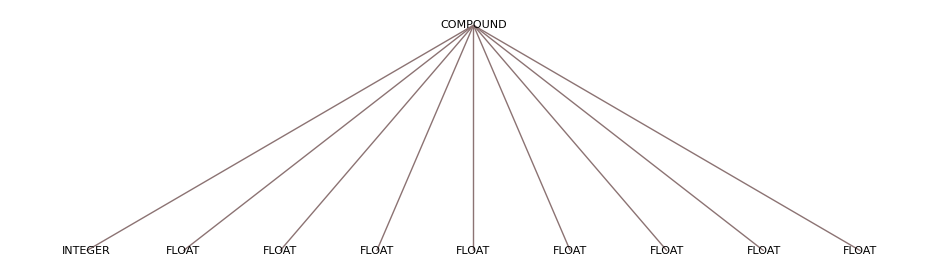

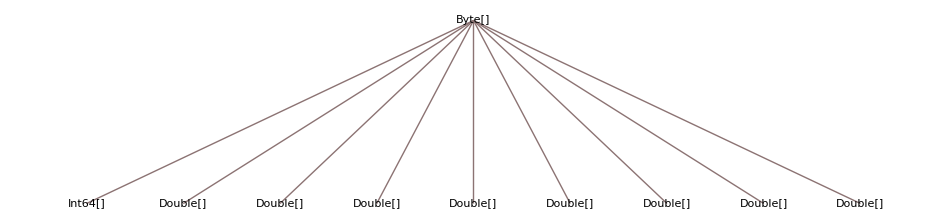

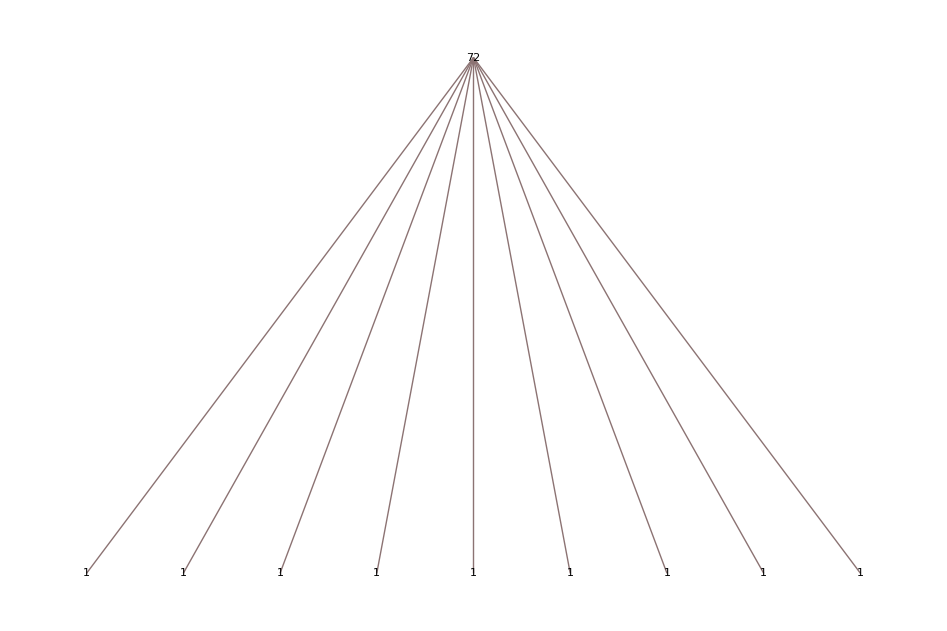

```mathematica
CompoundDataTypeInformationTree["011305_AnalysisCycleLevel.hdf5",imp[[1001]]]
```

```mathematica
datgd=ReadRowRank2["011305_AnalysisCycleLevel.hdf5",StringJoin[imp[[1001]]]]
Dimensions[datgd=ReadRank1["011305_AnalysisCycleLevel.hdf5",StringJoin[imp[[1001]]]]]
```

ReadRowRank2[011305_AnalysisCycleLevel.hdf5,/Run011305/Neutron/NeutronCountsWithSpikeRemoval]

{476,1,9,8}

```mathematica
datgd[[1]][[1]]
Dimensions[datgd[[1]][[1]]]
datgd[[1]][[1]][[4]]
```

{{1,0,0,0,0,0,0,0},{0,0,0,0,128,218,200,64},{0,0,0,0,0,206,184,64},{58,86,205,20,166,99,213,63},{0,0,0,0,8,123,2,65},{225,75,42,113,135,51,92,64},{102,110,243,245,245,235,83,64},{72,22,36,96,165,243,123,63},{51,120,233,4,123,81,120,64}}

{9,8}

{58,86,205,20,166,99,213,63}

```mathematica
Normal[ByteArray["AQIDBAUGBwg="]]
```

{1,2,3,4,5,6,7,8}

```mathematica
(*12725*)
datgd[[1]][[1]][[2]]
```

{0,0,0,0,128,218,200,64}

```mathematica
Needs["h5mma`"]
??h5mma`*
```

```mathematica
ImportHDF
```

ImportHDF5[011305_AnalysisCycleLevel.hdf5]

```mathematica
ImportHDF5["011305_AnalysisCycleLevel.hdf5","Data"]
```

ImportHDF5[011305_AnalysisCycleLevel.hdf5,Data]